# Séance M 1 (Title)

## One-liners (Subtitle)

Introduction à l’organisation de l’interface
Nom Prénom : xxxdi xx mois année (Subsubtitle)

## 1. Mise en Forme Générale (section)

### A. L’interface (sous-section)

#### 1. sous-sous-section n°1

texte
texte : la cellule ci dessous est une cellule d”Input”

```mathematica
3+5
```

8

#### 2. sous-sous-section n°2

texte
texte : la cellule ci-dessous est une autre cellule d”Input”

```mathematica
4+6
```

10

### B. Le noyau (sous-section)

#### 1. sous-sous-section

texte

## II. Mise en Forme spécifique

### 1. Saisie

#### I. Avec la palette Texte (Writing Assistant)

Dans une cellule “Texte” saisir les formules :
∑_(i=1)^10 i,	∑_(i=1)^n i,	(1 | 2
3 | 4)
(NB: utiliser Tab pour passer d’une case à l’autre)

# Suite TME :

## A. Opérations de base (symboliques avec précision arbitraire)

```mathematica
Cos[Pi](* Mathematica connait les regles de trigonometrie donc il recalcule ! *)
```

-1

```mathematica
N[Pi,10]
```

3.141592654

```mathematica
{Cos[x], x^2, x+2} /. x-> Pi
```

{-1,π^2,2+π}

```mathematica
3x+2x
```

5 x

```mathematica
3^100
```

515377520732011331036461129765621272702107522001

```mathematica
True || False
```

False

```mathematica
True && !False
```

True

```mathematica
3^100; //AbsoluteTiming
```

{0.0000439,Null}

```mathematica
3^10000;//AbsoluteTiming
```

{0.0000379,Null}

## B. Opérations de base (numériques)

```mathematica
(10.2 - 3.1)*6.2/2.9
```

```mathematica
15.17930344827588
```

```mathematica
(2+3I)*(4-5I)
```

23+2 ⅈ

## C. Nombres et Fonctions élémentaires

```mathematica
N[Pi]
```

3.14159

```mathematica
e
```

e

```mathematica
N[E]
```

2.71828

```mathematica
N[Infinity]
```

∞

```mathematica
N[I]
```

0.+1. ⅈ

```mathematica
{E^x, Sqrt[x], Ln[x], Log[x], Abs[x], Factorial[x]} /. x-> 1
```

{ⅇ,1,Ln[1],0,1,1}

## D. Fonctions

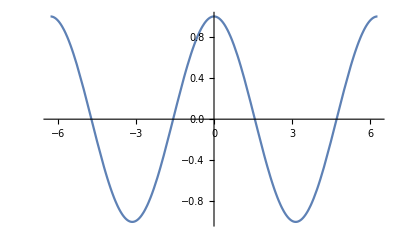

```mathematica
Plot[
Cos[x],
{x, -2Pi, 2Pi}
]
```

```mathematica
Manipulate[
Plot[
Cos[ax+b],
{x, -2Pi,2Pi}
],
{a, 1, 10},
{b, 0, 2Pi}
]
```

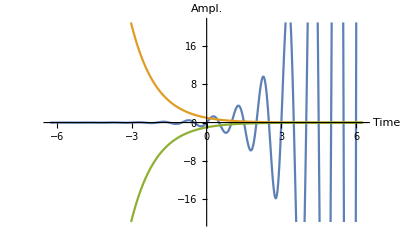

```mathematica
Plot[
{E^x*Sin[2Pi*x], Exp[-x], -Exp[-x]},
{x, -2Pi, 2Pi},
AxesLabel->{"Time", "Ampl."}
]
```

```mathematica
h[x_] = ax^4/(b+x^3)
```

ax^4/(b+x^3)

```mathematica
Manipulate[Plot[ax^4/(b+x^3),{x,-8,8}],{ax,-8,8},{b,-2,2}]
```

```mathematica
ResourceFunction["InflectionPoints"][ax^4/(b+x^3),x]
```

[ax^4/(b+x^3),x]

[ax^4/(b+x^3),x]

```mathematica
D[ax^4/(b+x^3), x]
```

-(5 (b+x^3)^2)/(3 ax^4 x^2)

```mathematica
∂_x ∂_x ∂_x ∂_x ∂_x ax^4/(b+x^3) (* dérivée 5eme *)
```

-(29160 ax^4 x^10)/((b+x^3)^6)+(38880 ax^4 x^7)/((b+x^3)^5)-(12960 ax^4 x^4)/((b+x^3)^4)+(720 ax^4 x)/((b+x^3)^3)

```mathematica
Solve[h[s] == a/2, s]
```

{{s→((2 ax^4-a b)^(1/3))/a^(1/3)},{s→-((-1)^(1/3) (2 ax^4-a b)^(1/3))/a^(1/3)},{s→((-1)^(2/3) (2 ax^4-a b)^(1/3))/a^(1/3)}}

## E. Graphiques 2D, 3D, sons et animations